```mathematica
Clear["W`ICA`*"]
<<ICA`;
Names["W`ICA`*"]
```

{Epsilon,fastICA,maxNumIterations,retW,Whiten}

```mathematica
MaxMemoryUsed[]
```

15382900

## Use image data to test:

```mathematica
p1=-Graphics-;
p2=-Graphics-;
p3=-Graphics-;
```

```mathematica
(*ImageData[p1]
Dimensions[%]*)
```

{«1»}

{192,192}

```mathematica
ImageResize[p1,80]
```

-Graphics-

```mathematica
imagesToData[images_]:=Module[{nbIm,nbCol,newIm},
nbIm=Length[images];
nbCol=Dimensions[images][[3]];
newIm=Table[Flatten[images[[i]],1],{i,nbIm}];
Return[newIm];
];
```

```mathematica
(*dp1=imagesToData[{ImageData[p1]}];*)
dp=imagesToData[{ImageData[ImageResize[p1,50]],ImageData[ImageResize[p2,50]],ImageData[ImageResize[p3,50]]}];
Dimensions[dp]
```

{3,2500}

```mathematica
(*Export["..\\tmp\\Tmp_pic.Mat",dp];
ipc=Import["..\\tmp\\pci_i.mat"][[1]];
ipc[[1,;;50]]*)
```

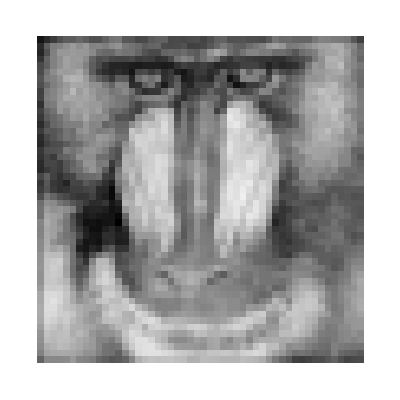
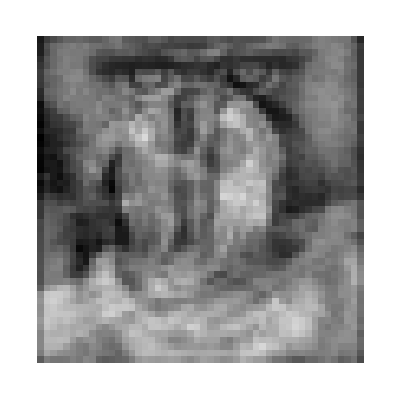
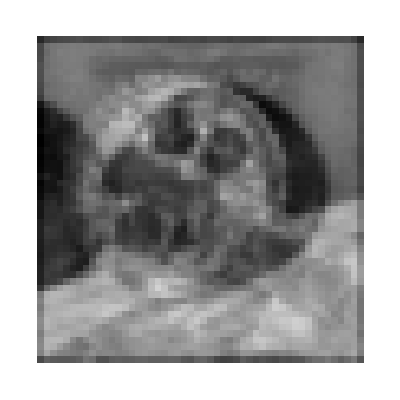

```mathematica
nbCol=50;
Table[ArrayPlot[Partition[dp[[i]],nbCol]],{i,3}]
```

192

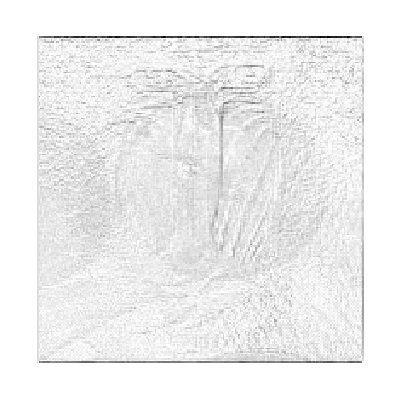
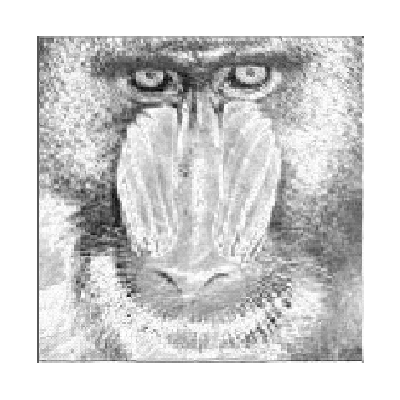
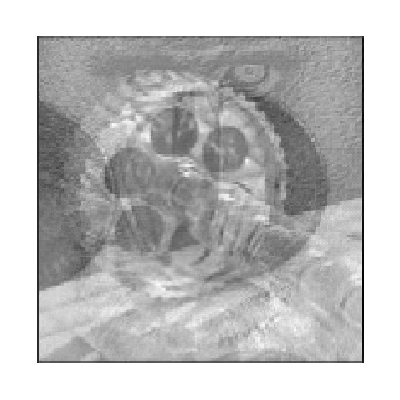

```mathematica
nbCol=192
Table[ArrayPlot[Partition[ipc[[i]],nbCol]],{i,3}]
```

```mathematica
Correlation[ipc];
```

```mathematica
(*If we use pixels as signals,then the features of each pic came out...,translate original 2500 pixels into several features*)
```

```mathematica
dp0=dp;
{pic,W,A}=fastICA[dp0ᵀ,retW->True];
```

use deltaW:1/1000, Maxstep:100

using opimized method for whiten

Dimension adjusted to 2 according to covariance matrix

Sum of 2498 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 0.960626

Largest remaining (non-zero) eigenvalue 20.928

whiten OK

guess OK

total time:0.0625seconds

```mathematica
Dimensions[pic]
picᵀ/Norm[picᵀ];
Dimensions[dpᵀ]
Dimensions[W]
```

{2,3}

{2500,3}

{2,2500}

```mathematica
pic
```

{{-8.42949,-7.42463,-9.42462},{-4.79788,-3.06864,-3.06302}}

```mathematica
Dimensions[A]
```

{2500,2}

```mathematica
A.pic
```

{{-0.530287,-0.530287,-0.530287},{-0.277022,-0.277022,-0.277022},«2497»,{-0.433178,-0.433178,-0.433178}}

```mathematica
pic==W.dp0ᵀ
```

True

```mathematica
dp0.dp0ᵀ//MatrixForm
pic.picᵀ//MatrixForm
```

(490.073 | 482.019 | 507.489
482.019 | 494.975 | 538.353
507.489 | 538.353 | 608.479)

(23546.3 | -17278.5 | 4870.55
-17278.5 | 16683.5 | -3998.41
4870.55 | -3998.41 | 3626.09)

```mathematica
(* for projection, center first*)
```

```mathematica
cdp0=Standardize[dp0ᵀ,Mean,1&]ᵀ;
```

```mathematica
cdp0.picᵀ/A
```

{{2499.,2499.,2499.},{2499.,2499.,2499.},{2499.,2499.,2499.}}

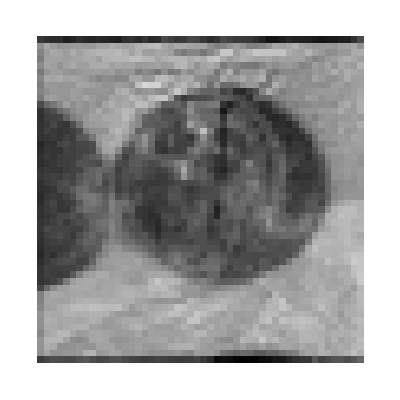
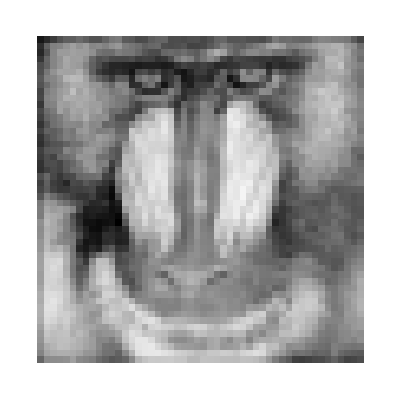
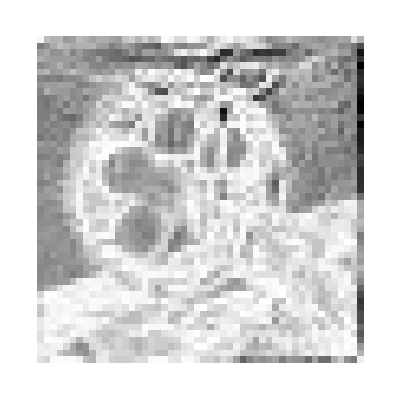

```mathematica
Table[ArrayPlot[Partition[pic[[i]],50]],{i,3}]
```

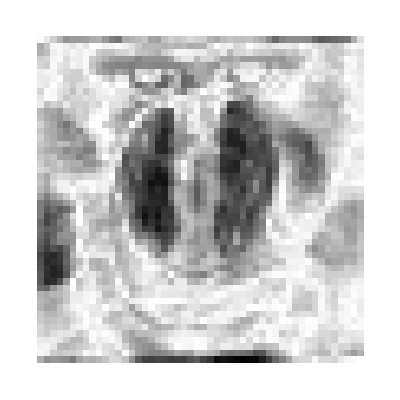
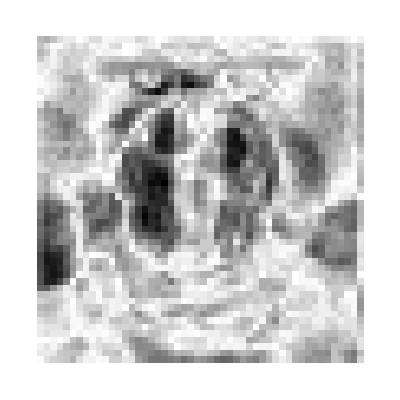

```mathematica
Table[ArrayPlot[Partition[Aᵀ[[i]],50]],{i,2}]
```

### another two pics

```mathematica
p1=Import["..\\tmp\\a1.bmp","GrayLevels"];
p2=Import["..\\tmp\\a2.bmp","GrayLevels"];
dp=imagesToData[{p1,p2}];
Dimensions[dp]
```

{2,26800}

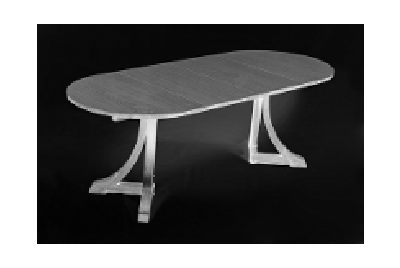
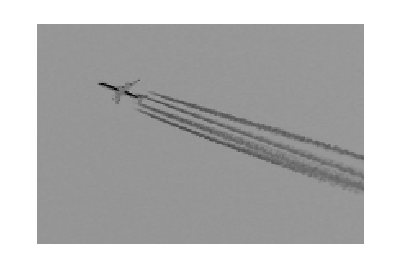

```mathematica
Table[ArrayPlot[Partition[dp[[i]],200]],{i,2}]
```

```mathematica
a=Table[RandomReal[{0,1}],{3},{2}];
```

```mathematica
a
```

{{0.522481,0.716097},{0.366702,0.910983},{0.810147,0.461915}}

```mathematica
mp=a.dp;
(*Dimensions[mp]
Export["..\\tmp\\mp.mat",mp];*)
```

{3,26800}

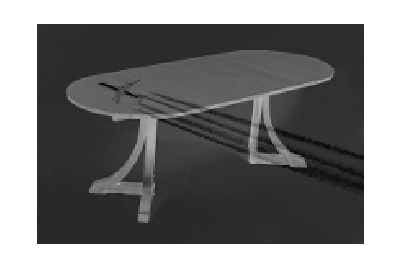
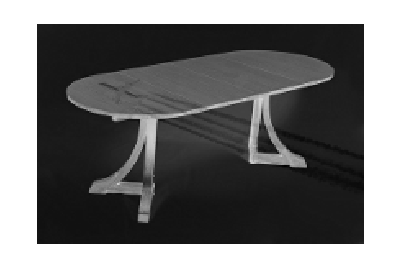
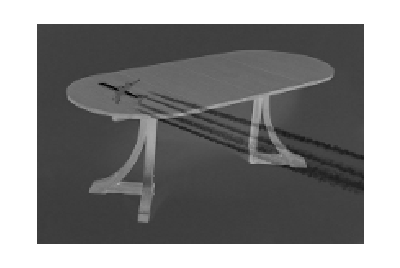

```mathematica
Table[ArrayPlot[Partition[mp[[i]],200]],{i,3}]
```

```mathematica
icm=fastICA[mp];
```

use deltaW:1/1000, Maxstep:100

Dimension adjusted to 2 according to covariance matrix

Smallest remaining (non-zero) eigenvalue 0.000490214

Largest remaining (non-zero) eigenvalue 0.0335955

Sum of 1 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

whiten OK

guess OK

total time:0.125seconds

```mathematica
(*Correlation[icmᵀ]*)
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

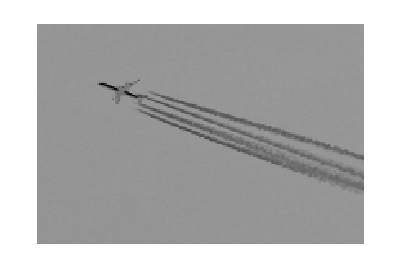
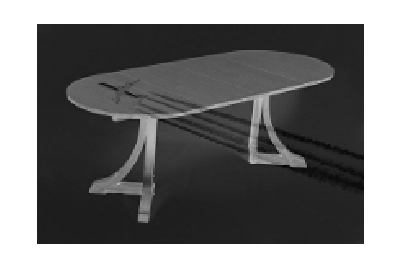

```mathematica
Table[ArrayPlot[Partition[icm[[i]],200]],{i,2}]
```

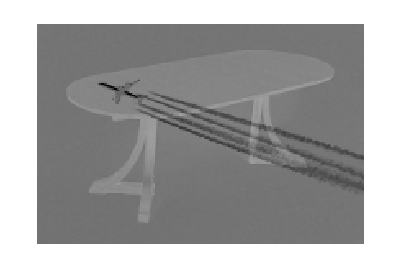

```mathematica
ArrayPlot[Partition[icm[[2]]+icm[[1]],200]]
```

```mathematica
(*icm2=Import["..\\tmp\\matlab.mat"][[1]];*)(* this is a matlab version*)
```

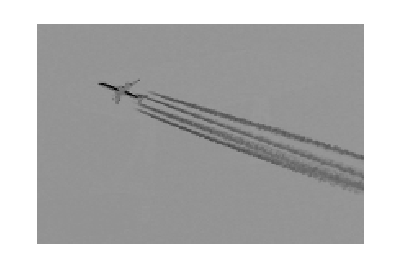
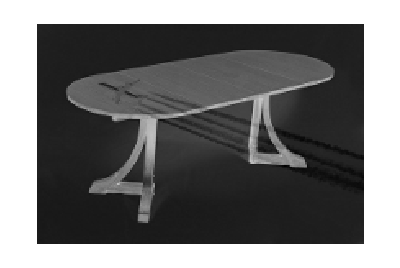

```mathematica
Table[ArrayPlot[Partition[icm2[[i]],200]],{i,2}]
```

```mathematica
Correlation[icm2ᵀ]
```

{{1.,-9.84007×10^-15},{-9.84007×10^-15,1.}}